## Init

```mathematica
AppendTo[$Path,ParentDirectory@NotebookDirectory[]];
Needs["AstronomicalDiaries`"]
```

```mathematica
$ADBase=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Data"}];
```

```mathematica
inferencingSamplesDir=FileNameJoin[{ParentDirectory@NotebookDirectory[],"InferencingSamples"}];
```

```mathematica
importChains[path_]:=FromTabular[Import[#,"Tabular"],"Rows"]&/@Sort@FileNames["*.parquet",path]
```

```mathematica
observations=ADObservations[];
```

```mathematica
Needs["AstronomicalDiaries`Astronomy`"]
```

```mathematica
Needs["AstronomicalDiaries`Dataset`Names`"]
```

### Figures

```mathematica
figDir=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Figures"}];
```

```mathematica
exportFig[name_,fig_]:=(
Export[FileNameJoin[{figDir,name<>".pdf"}],fig];
Export[FileNameJoin[{figDir,"Dark",name<>".png"}],Rasterize[fig,Background->None,LightDark->"Dark",RasterSize->2000]];
)
```

### Constants

```mathematica
allMonths={"I","II","III","IV","V","VI","VI2","VII","VIII","IX","X","XI","XII","XII2"};
```

```mathematica
allTimeCategories={"BeginningOfTheNight","FirstPartOfTheNight"(*,"MiddlePartOfTheNight"*),"LastPartOfTheNight"};
```

### Colors

```mathematica
timeCategoryColors=AssociationThread[allTimeCategories,ColorData[116]/@Range[Length[allTimeCategories]]];
```

## Before model

### Previewing observations

```mathematica
p=With[{nameReferences=GroupBy[Normal@referenceNames,Last->First,First]},
Dataset[
ReplacePart[#,"Reference"->nameReferences[#Reference]]&/@
Select[observations,#TextID==="X102782"&][[All,{"Line","RegnalYear","Month","EarliestDay","LatestDay","Time","Object","Cubits","Fingers","Relation","Reference"}]],
MaxItems->{Infinity,Infinity},
ItemSize->{{All,"Line"}->4,{All,"Time"}->14,{All,"Object"}->5,{All,"Cubits"}->5,{All,"Relation"}->7,{All,"Reference"}->9}
]
]
```

```mathematica
exportFig["X102782",p]
```

### Scatter plots

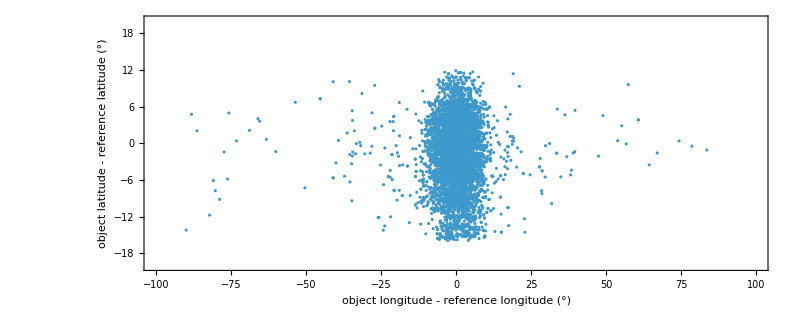

```mathematica
p=ListPlot[Reverse@objectDisplacement[#Object,#Reference,DateObject[#Date,"Instant",TimeZone->$timeZone]]&/@
Select[observations,!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&],
PlotRange->{{-100,100},{-20,20}},
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"object longitude - reference longitude (°)","object latitude - reference latitude (°)"},
ImageSize->800
]
```

```mathematica
exportFig["basic_scatter",p]
```

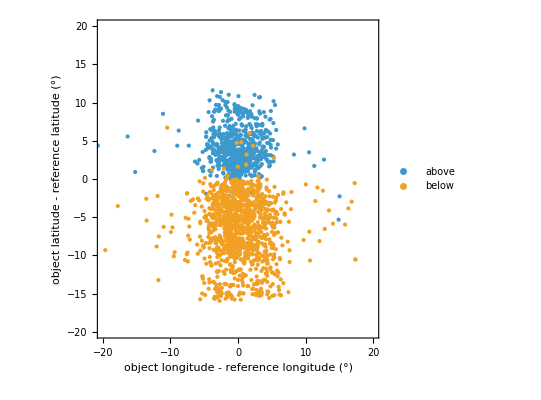

```mathematica
p1=ListPlot[
Lookup[
GroupBy[
{#Relation,Reverse@objectDisplacement[#Object,#Reference,DateObject[#Date,"Instant",TimeZone->$timeZone]]}&/@
Select[observations,!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&],
First->Last
],
{"Above","Below"}
],
PlotLegends->Placed[{"above","below"},Above],
PlotRange->{{-20,20},{-20,20}},
PlotStyle->PointSize[Small],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"object longitude - reference longitude (°)","object latitude - reference latitude (°)"},
ImageSize->{Automatic,250}
]
```

```mathematica
exportFig["above_below_scatter",p1]
```

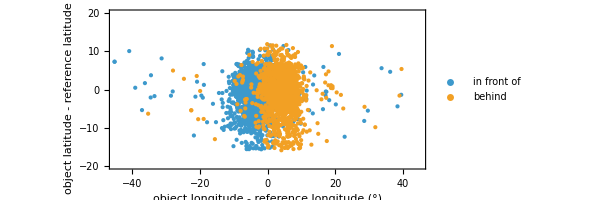

```mathematica
p2=ListPlot[
Lookup[
GroupBy[
{#Relation,Reverse@objectDisplacement[#Object,#Reference,DateObject[#Date,"Instant",TimeZone->$timeZone]]}&/@
Select[observations,!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&],
First->Last
],
{"InFrontOf","Behind"}
],
PlotLegends->Placed[{"in front of","behind"},Above],
PlotRange->{{-45,45},{-20,20}},
PlotStyle->PointSize[Small],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"object longitude - reference longitude (°)","object latitude - reference latitude (°)"},
ImageSize->{Automatic,250}
]
```

```mathematica
exportFig["infrontof_behind_scatter",p2]
```

### Dates and times

```mathematica
monthTimeCategories=GroupBy[observations,Lookup["Month"],Counts[#[[All,"Time"]]]&];
```

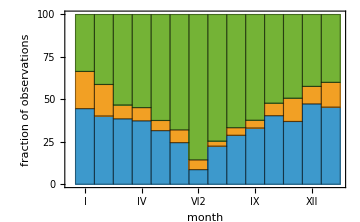

```mathematica
p=BarChart[
Lookup[Lookup[allTimeCategories]/@monthTimeCategories,allMonths],
ChartLabels->{allMonths,None},
ChartLayout->"Percentile",
ChartLegends->Placed[SwatchLegend[Automatic,Style[#,10]&/@allTimeCategories,LegendLayout->(Row[Row[#,Spacer[0]]&/@#,Spacer[5]]&)],Above],
(*ChartLegends->Placed[allTimeCategories,Above],*)
ChartStyle->Lookup[timeCategoryColors,allTimeCategories],
BarSpacing->None,
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameLabel->{"month","fraction of observations"},
ImageSize->Medium
]
```

```mathematica
exportFig["month_time_cats_fractions",p]
```

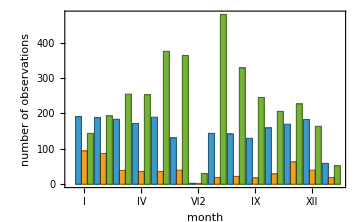

```mathematica
p=BarChart[
Lookup[Lookup[allTimeCategories]/@monthTimeCategories,allMonths],
ChartLabels->{allMonths,None},
ChartLayout->"Grouped",
ChartStyle->Lookup[timeCategoryColors,allTimeCategories],
BarSpacing->None,
Frame->True,
FrameLabel->{"month","number of observations"},
ImageSize->Medium
]
```

```mathematica
exportFig["month_time_cats_counts",p]
```

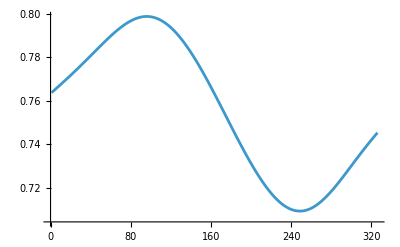

```mathematica
ListLinePlot[{
DateValue[#,"DayFraction"]&/@Sunset[Entity["HistoricalSite","Babylon::b5wkm"]["Position"],DateRange[ADChronology[][{1,"I"}],ADChronology[][{1,"XII"}]],TimeZone->$timeZone]["Values"]
}]
```

## After model

### Importing samples

#### Base

```mathematica
modelObservations=Select[observations,!#Damaged&&!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&&!MissingQ[#Relation]&&!(MissingQ[#Cubits]&&MissingQ[#Fingers])&];
```

```mathematica
chains=importChains[FileNameJoin[{inferencingSamplesDir,"base"}]];
samples=Catenate@chains[[All,500;;]];
```

#### Missing days

```mathematica
modelObservationsMissingDays=Select[observations,!#Damaged&&!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#EarliestDate]&&!MissingQ[#LatestDate]&&!MissingQ[#SEYear]&&!MissingQ[#Month]&&!MissingQ[#Relation]&&!(MissingQ[#Cubits]&&MissingQ[#Fingers])&];
```

```mathematica
chainsMissingDays=importChains[FileNameJoin[{inferencingSamplesDir,"missingDays"}]];
samplesMissingDays=Catenate@chainsMissingDays[[All,500;;]];
```

#### Masked years

```mathematica
getYearMaskedObservations[observations_,seYear_]:=Join[#,<|"SEYear"->Missing["Unknown",seYear]|>]&/@Select[observations,#SEYear===seYear&]
```

```mathematica
modelObservationsMaskedYears=Join[modelObservations,
getYearMaskedObservations[modelObservations,117],
getYearMaskedObservations[modelObservations,232],
getYearMaskedObservations[modelObservations,158],
getYearMaskedObservations[modelObservations,-59],
getYearMaskedObservations[modelObservations,-67]
];
```

```mathematica
chainsMaskedYears=importChains[FileNameJoin[{inferencingSamplesDir,"maskedYears"}]];
samplesMaskedYears=Catenate@chainsMaskedYears[[All,500;;]];
```

#### SE 117

```mathematica
modelObservations117=Join[modelObservations,
Select[getYearMaskedObservations[modelObservations,117],#TextID==="X201941"&]/.Missing["Unknown",117]->Missing["Unknown",{117,"X201941"}],
Select[getYearMaskedObservations[modelObservations,117],#TextID==="X201942"&]/.Missing["Unknown",117]->Missing["Unknown",{117,"X201942"}]
];
```

```mathematica
chains117=importChains[FileNameJoin[{inferencingSamplesDir,"se117"}]];
samples117=Catenate@chains117[[All,500;;]];
```

### Cubit length

```mathematica
Around[1/samples[[All,"l"]]]
```

2.4260.011

```mathematica
Median[1/samples[[All,"l"]]]
```

2.42559

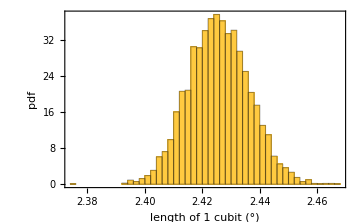

```mathematica
p=Histogram[
1/samples[[All,"l"]],{0.002},"PDF",
Frame->True,
FrameLabel->{"length of 1 cubit (°)","pdf"},
ImageSize->Medium
]
```

```mathematica
exportFig["cubit_length_hist",p]
```

### Observation accuracy

```mathematica
Sqrt@Around@samples[[All,"sigma2"]]
```

0.5120.010

```mathematica
Sqrt@samples[[-1,"sigma2"]]/samples[[-1,"l"]]
```

1.24625

```mathematica
Around@Sqrt@samples[[All,"sigma2"]]/Around@samples[[All,"l"]]
```

1.2420.026

```mathematica
Around[Sqrt@samples[[All,"sigma2"]]/samples[[All,"l"]]]
```

1.2420.026

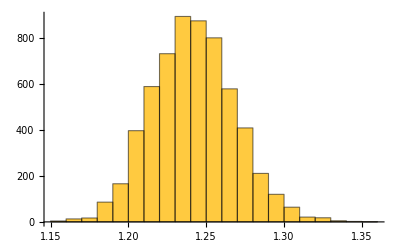

```mathematica
Histogram[Sqrt@samples[[All,"sigma2"]]/samples[[All,"l"]],{0.01}]
```

### Observation times

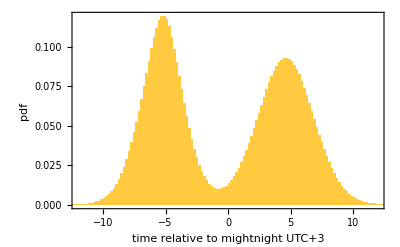

```mathematica
p=Histogram[
Flatten@samples[[All,"t"]],{0.2},"PDF",
PlotRange->{{-12,12},All},
Frame->True,
PlotRangeClipping->True,
FrameLabel->{"time relative to mightnight UTC+3","pdf"},
ImageSize->{Automatic,200}
]
```

```mathematica
exportFig["observation_times",p]
```

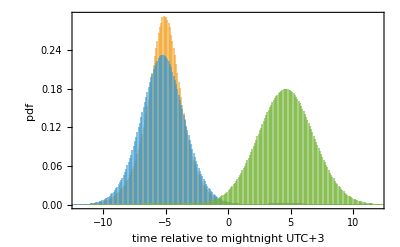

```mathematica
p=With[{timeCats={"FirstPartOfTheNight","BeginningOfTheNight","LastPartOfTheNight"}},
Histogram[
Lookup[GroupBy[Catenate@Transpose[{samples[[All,"timeCats"]],samples[[All,"t"]]},1<->3],First->Last],timeCats],
{0.1},
"PDF",
ChartLegends->Placed[SwatchLegend[Automatic,Style[#,8.5]&/@timeCats,LegendLayout->(Row[Row[#,Spacer[0]]&/@#,Spacer[5]]&)],Above],
ChartStyle->Lookup[timeCategoryColors,timeCats],
PlotRange->{{-12,12},All},
Frame->True,
FrameLabel->{"time relative to mightnight UTC+3","pdf"},
ImageSize->{Automatic,200}
]
]
```

```mathematica
exportFig["observation_times_by_cat",p]
```

### Scatter plots with accurate times

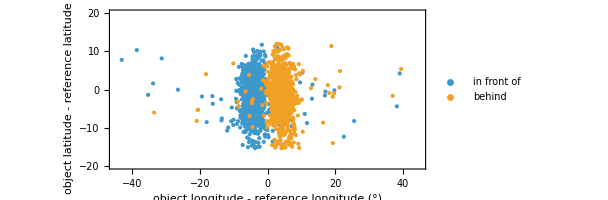

```mathematica
p=With[{mask=!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&/@modelObservations},
ListPlot[
Lookup[
GroupBy[
MapThread[
{#Relation,Reverse@objectDisplacement[#Object,#Reference,DateObject[#Date,"Instant",TimeZone->$timeZone]+Quantity[#2,"Hours"]]}&,
{
Pick[modelObservations,mask],
Pick[Mean@samples[[All,"t"]],mask]
}
],
First->Last
],
{"InFrontOf","Behind"}
],
PlotLegends->Placed[{"in front of","behind"},Above],
PlotRange->{{-45,45},{-20,20}},
PlotStyle->PointSize[Small],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"object longitude - reference longitude (°)","object latitude - reference latitude (°)"},
ImageSize->{Automatic,250}
]
]
```

```mathematica
exportFig["infrontof_behind_scatter_accurate",p]
```

### Outlier plot

```mathematica
trueDistances=Around/@AstronomicalDiaries`Modeling`TrueModel`objectDistanceApprox[
modelObservations[[All,"Object"]],
modelObservations[[All,"Reference"]],
modelObservations[[All,"Relation"]],
modelObservations[[All,"Date"]],
Transpose@samples[[All,"t"]]
];
```

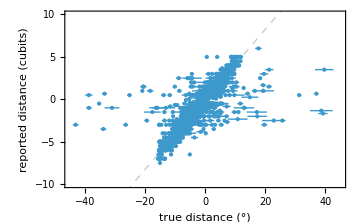

```mathematica
ListPlot[
Transpose[{
trueDistances,
N@*AstronomicalDiaries`Astronomy`observationCubitsSigned/@modelObservations
}],
Epilog->{Opacity[0.2],Dashed,InfiniteLine[{0,0},{1/Mean@samples[[All,"l"]],1}]},
AspectRatio->1/GoldenRatio,
PlotStyle->PointSize[Small],
PlotLegends->Automatic,
PlotRange->{{-45,45},{-10,10}},
PlotRangeClipping->True,
Frame->True,
FrameLabel->{"true distance (°)","reported distance (cubits)"},
Axes->None,
ImageSize->Medium
]
```

```mathematica
p=PointValuePlot[
Transpose[{
trueDistances,
N@*AstronomicalDiaries`Astronomy`observationCubitsSigned/@modelObservations
}]->Mean@samples[[All,"m"]],
Epilog->{Opacity[0.2],Dashed,InfiniteLine[{0,0},{1/Mean@samples[[All,"l"]],1}]},
AspectRatio->1/GoldenRatio,
PlotStyle->PointSize[Small],
PlotLegends->Automatic,
PlotRange->{{-45,45},{-10,10}},
PlotRangeClipping->True,
Frame->True,
FrameLabel->{"true distance (°)","reported distance (cubits)"},
ImageSize->Medium
]
```

-Graphics-

```mathematica
exportFig["outlier_plot",p]
```

### Day imputation

```mathematica
dayRangePlot[id_]:=
With[
{idx=SelectFirst[modelObservationsMissingDays,#ID===id&->"Index"]},
{deltaD=samplesMissingDays[[All,"deltaD",idx]]},
ListPlot[
Normalize[
Lookup[Counts[deltaD],Range[0,Max[deltaD]],0],
Total
],
PlotLabel->modelObservationsMissingDays[[idx,"ID"]],
PlotRange->{All,{0,All}},
Filling->Bottom,
Frame->True,
FrameLabel->{"day in range","probability"},
ImageSize->250
]
]
```

```mathematica
SelectFirst[observations,#ID==={"X301120",{1729,1769}}&]
```

<|ID→{X301120,{1729,1769}},Object→Moon,Relation→InFrontOf,Reference→Alcyone,Cubits→4,Fingers→Missing[],Time→Missing[],Day→Missing[],EarliestDay→4,LatestDay→30,Month→VIII,RegnalYear→{SE,199},SEYear→199,Date→Missing[],EarliestDate→Sat 30 Oct 113 BCJulian,LatestDate→Thu 25 Nov 113 BCJulian,Damaged→False,Line→o 20',TextID→X301120,Range→{1729,1769},TimeRange→Missing[],EarliestDayRange→{1605,1609},LatestDayRange→Missing[]|>

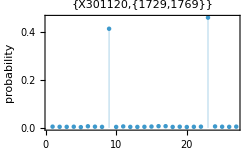

```mathematica
p=dayRangePlot@{"X301120",{1729,1769}}
```

```mathematica
exportFig["day_range_X301120",p]
```

```mathematica
SelectFirst[observations,#ID==={"X201706",{640,685}}&]
```

<|ID→{X201706,{640,685}},Object→Moon,Relation→South,Reference→Alpherg,Cubits→3/2,Fingers→Missing[],Time→Missing[],Day→Missing[],EarliestDay→7,LatestDay→30,Month→VIII,RegnalYear→{SE,141},SEYear→141,Date→Missing[],EarliestDate→Thu 14 Nov 171 BCJulian,LatestDate→Sat 7 Dec 171 BCJulian,Damaged→False,Line→o 6,TextID→X201706,Range→{640,685},TimeRange→Missing[],EarliestDayRange→{542,546},LatestDayRange→Missing[]|>

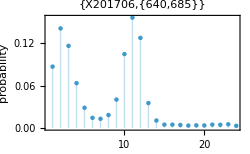

```mathematica
p=dayRangePlot@{"X201706",{640,685}}
```

```mathematica
exportFig["day_range_X201706",p]
```

```mathematica
SelectFirst[observations,#ID==={"X102613",{2110,2140}}&]
```

<|ID→{X102613,{2110,2140}},Object→Mars,Relation→Above,Reference→Saturn,Cubits→Missing[],Fingers→3,Time→LastPartOfTheNight,Day→Missing[],EarliestDay→5,LatestDay→13,Month→VIII,RegnalYear→{SE,50},SEYear→50,Date→Missing[],EarliestDate→Sun 29 Oct 262 BCJulian,LatestDate→Mon 6 Nov 262 BCJulian,Damaged→False,Line→o 14,TextID→X102613,Range→{2110,2140},TimeRange→{2086,2107},EarliestDayRange→{1980,1993},LatestDayRange→{2184,2189}|>

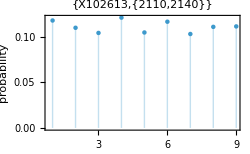

```mathematica
p=dayRangePlot@{"X102613",{2110,2140}}
```

```mathematica
exportFig["day_range_X102613",p]
```

### Year imputation

```mathematica
yearImputationPlot[counts_,true_,opts___]:=
ListPlot[
If[#[[1]]===true,Style[#,Red],#]&/@KeyValueMap[List,Normalize[<|true->0,counts|>,Total]],
opts,
PlotRange->{MinMax@Keys[ADChronology[]][[All,1]],{0,(*1*)All}},
Filling->Bottom,
FillingStyle->Directive[Thickness[0.007]],
PlotStyle->PointSize[0.015],
Frame->True,
FrameLabel->{"year (SE)","probability"},
Axes->False,
PlotLabel->StringTemplate["SE ``"][true]
]
```

```mathematica
missingYearIndices=KeySelect[PositionIndex[modelObservationsMaskedYears[[All,"SEYear"]]][[All,1]],MissingQ];
```

```mathematica
Length@getYearMaskedObservations[modelObservations,-67]
```

8

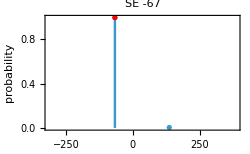

```mathematica
p=yearImputationPlot[
Counts@samplesMaskedYears[[All,"years",missingYearIndices[Missing["Unknown",-67]]]],
-67,
ImageSize->250
]
```

```mathematica
exportFig["year_imputation_-67",p]
```

```mathematica
Length@getYearMaskedObservations[modelObservations,232]
```

7

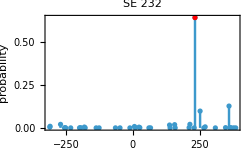

```mathematica
p=yearImputationPlot[
Counts@samplesMaskedYears[[All,"years",missingYearIndices[Missing["Unknown",232]]]],
232,
ImageSize->250
]
```

```mathematica
exportFig["year_imputation_232",p]
```

```mathematica
Length@getYearMaskedObservations[modelObservations,-59]
```

2

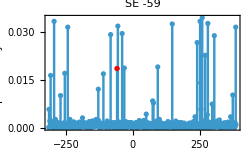

```mathematica
p=yearImputationPlot[
Counts@samplesMaskedYears[[All,"years",missingYearIndices[Missing["Unknown",-59]]]],
-59,
ImageSize->250
]
```

```mathematica
exportFig["year_imputation_-59",p]
```

#### SE 117

```mathematica
modelObservations117=Join[modelObservations,
Select[getYearMaskedObservations[modelObservations,117],#TextID==="X201941"&]/.Missing["Unknown",117]->Missing["Unknown",{117,"X201941"}],
Select[getYearMaskedObservations[modelObservations,117],#TextID==="X201942"&]/.Missing["Unknown",117]->Missing["Unknown",{117,"X201942"}]
];
```

```mathematica
chains117=importChains[FileNameJoin[{inferencingSamplesDir,"se117"}]];
samples117=Catenate@chains117[[All,500;;]];
```

```mathematica
missingYearIndices117=KeySelect[PositionIndex[modelObservations117[[All,"SEYear"]]][[All,1]],MissingQ];
```

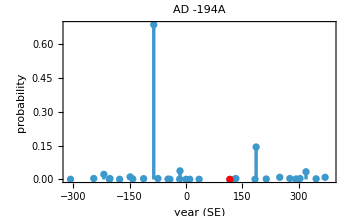

```mathematica
p=yearImputationPlot[Counts[samples117[[All,"years",missingYearIndices117[Missing["Unknown",{117,"X201941"}]]]]],
117,
PlotLabel->"AD -194A",
ImageSize->350
]
```

```mathematica
exportFig["year_imputation_117A",p]
```

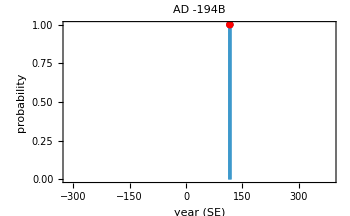

```mathematica
p=yearImputationPlot[Counts[samples117[[All,"years",missingYearIndices117[Missing["Unknown",{117,"X201942"}]]]]],
117,
PlotLabel->"AD -194B",
ImageSize->350
]
```

```mathematica
exportFig["year_imputation_117B",p]
```